```mathematica
data=Import["D:\\data_parallel.DAT"]
```

{{254.696,133.736},{306.461,126.119},{328.081,121.886},{362.011,128.658},{396.355,126.965},{422.59,115.961},{431.487,109.19},{483.044,105.804},{491.858,100.726},{530.899,90.5683},{569.194,95.6469},{608.443,81.2576},{655.593,80.4111},{703.2,70.2539},{745.653,77.8718},{831.306,77.8718},{836.045,68.5611},{870.099,72.7932},{964.773,63.4825},{1041.57,69.4075}}

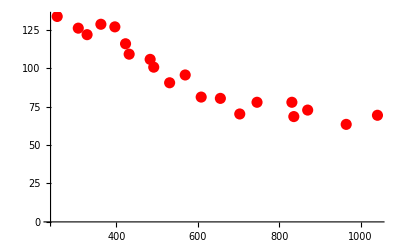

```mathematica
p0=ListPlot[data,PlotStyle->{Red,PointSize[0.02]}]
```

```mathematica
datLn=Table[{1/data[[i]][[1]],data[[i]][[2]]//Log},{i,data//Length}]
```

{{0.00392624,4.89587},{0.00326306,4.83722},{0.00304802,4.80309},{0.00276235,4.85716},{0.00252299,4.84391},{0.00236636,4.75326},{0.00231757,4.69309},{0.0020702,4.66159},{0.00203311,4.6124},{0.0018836,4.5061},{0.00175687,4.56066},{0.00164354,4.39762},{0.00152534,4.38715},{0.00142207,4.25212},{0.00134111,4.35506},{0.00120293,4.35506},{0.00119611,4.22772},{0.00114929,4.28762},{0.00103651,4.15076},{0.000960088,4.23999}}

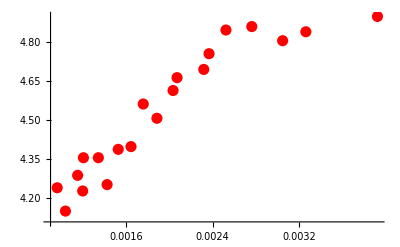

```mathematica
pp=ListPlot[datLn,PlotStyle->{Red,PointSize[0.02]}]
```

```mathematica
lm=LinearModelFit[datLn,{1,x},x]
```

FittedModel[3.97747+282.242 x]

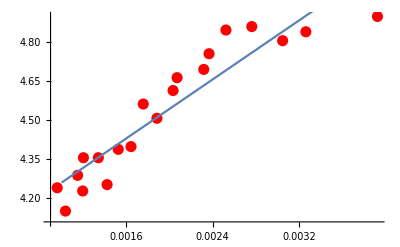

```mathematica
pl=Plot[lm[x],{x,0.001,0.004}];
Show[pp,pl]
```

```mathematica
lm["RSquared"]
```

0.868171

```mathematica
data=Import["D:\\data_perpendicular.DAT"]
```

{{277.083,463.845},{331.251,407.134},{358.935,366.505},{355.73,344.498},{373.565,330.109},{399.302,329.262},{396.428,300.484},{449.601,264.087},{475.173,266.626},{480.45,246.312},{562.193,238.694},{562.773,226.844},{610.462,214.994},{640.938,204.837},{696.737,202.297},{1154.1,132.89},{1231.68,122.733},{1257.79,114.268},{1318.12,106.651},{1374.25,97.3398},{1467.89,109.19},{1468.59,94.8005},{1511.83,86.3362},{1536.99,97.3398},{1576.24,82.9504},{1673.91,99.8791},{1768.88,84.6433},{1872.2,73.6397},{1983.71,70.2539}}

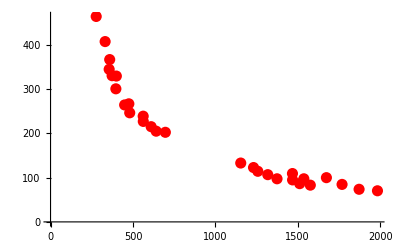

```mathematica
p01=ListPlot[data,PlotStyle->{Red,PointSize[0.02]}]
```

```mathematica
R=8.31;
T0=300;
nlm=NonlinearModelFit[data,A*((T/T0)^n)*Exp[-Eα/(R*T)],{A,n,Eα},T]
```

FittedModel[(21032.9 ⅇ^(«19»/T))/T^0.744477]

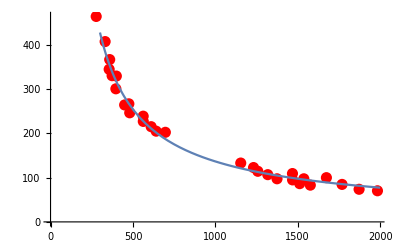

```mathematica
Show[ListPlot[data,PlotStyle->{Red,PointSize[0.02]}],Plot[nlm[T],{T,300,2000}]]
```

```mathematica
nlm["RSquared"]
```

0.997837